## Boson Quadratic Hamiltonian

## Calculating the Matrix Elements of H

## H_b=ϵb^+b-v(b^+b^++bb)

### Case |0>,|2>,|4>,...

```mathematica
dif[n_,m_]:=n-m;
matEl02[n_,m_,e_,v_]:=Piecewise[{{0, n==0&&m==0}, {e*m, dif[n,m]==0}, {√(m+1)√(m+2)*(-v), dif[n,m]==2}, {√m √(m-1)*(-v), dif[n,m]==-2}}];
```

```mathematica
Hmat02[n_,e_,v_]:=Table[Table[matEl02[2*(j-1),2*(i-1),e,v],{i,1,n}],{j,1,n}];
```

```mathematica
Hmat02[6,e,v]//MatrixForm
```

(0 | -√2 v | 0 | 0 | 0 | 0
-√2 v | 2 e | -2 √3 v | 0 | 0 | 0
0 | -2 √3 v | 4 e | -√30 v | 0 | 0
0 | 0 | -√30 v | 6 e | -2 √14 v | 0
0 | 0 | 0 | -2 √14 v | 8 e | -3 √10 v
0 | 0 | 0 | 0 | -3 √10 v | 10 e)

```mathematica
Hmat02[6,e,v]/e//MatrixForm
```

(0 | -(√2 v)/e | 0 | 0 | 0 | 0
-(√2 v)/e | 2 | -(2 √3 v)/e | 0 | 0 | 0
0 | -(2 √3 v)/e | 4 | -(√30 v)/e | 0 | 0
0 | 0 | -(√30 v)/e | 6 | -(2 √14 v)/e | 0
0 | 0 | 0 | -(2 √14 v)/e | 8 | -(3 √10 v)/e
0 | 0 | 0 | 0 | -(3 √10 v)/e | 10)

```mathematica
redM02[n_,q_]:=Hmat02[n,1,q];
```

### Case |1>,|3>,|5>,...

```mathematica
matEl13[n_,m_,e_,v_]:=Piecewise[{{0, n==0&&m==0}, {e*m, dif[n,m]==0}, {√(m+1)√(m+2)*(-v), dif[n,m]==2}, {√m √(m-1)*(-v), dif[n,m]==-2}}];
```

```mathematica
Hmat13[n_,e_,v_]:=Table[Table[matEl13[j-1,i-1,e,v],{i,1,n}],{j,1,n}];
```

```mathematica
Hmat13[6,e,v]//MatrixForm
```

(0 | 0 | -√2 v | 0 | 0 | 0
0 | e | 0 | -√6 v | 0 | 0
-√2 v | 0 | 2 e | 0 | -2 √3 v | 0
0 | -√6 v | 0 | 3 e | 0 | -2 √5 v
0 | 0 | -2 √3 v | 0 | 4 e | 0
0 | 0 | 0 | -2 √5 v | 0 | 5 e)

```mathematica
Hmat13[6,e,v]/e//MatrixForm
```

(0 | 0 | -(√2 v)/e | 0 | 0 | 0
0 | 1 | 0 | -(√6 v)/e | 0 | 0
-(√2 v)/e | 0 | 2 | 0 | -(2 √3 v)/e | 0
0 | -(√6 v)/e | 0 | 3 | 0 | -(2 √5 v)/e
0 | 0 | -(2 √3 v)/e | 0 | 4 | 0
0 | 0 | 0 | -(2 √5 v)/e | 0 | 5)

```mathematica
redM13[n_,q_]:=Hmat13[n,1,q];
```

## Solving the eigenvalue and eigenvector equation

## Case 1

```mathematica
redM02[4,q]//MatrixForm
```

(0 | -√2 q | 0 | 0
-√2 q | 2 | -2 √3 q | 0
0 | -2 √3 q | 4 | -√30 q
0 | 0 | -√30 q | 6)

```mathematica
Table[ListPlot[N[Eigenvalues[redM02[4,t]]],Joined->True,Axes->False,Frame->True,FrameLabel->{i,Subscript[λ, i]},PlotStyle->{Red,Thick},FrameStyle->Directive[Thick,Black],ImageSize->Medium,LabelStyle->{18,Bold}],{t,0.5,2,0.5}]
```

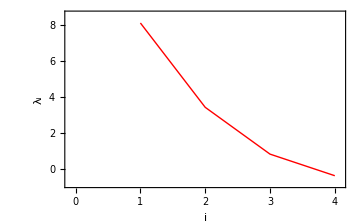
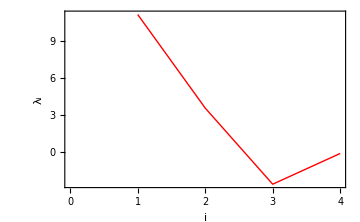
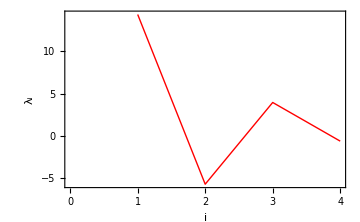
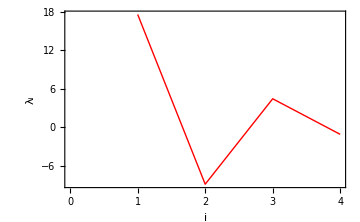

## Case 2

```mathematica
redM13[4,q]//MatrixForm
```

(0 | 0 | -√2 q | 0
0 | 1 | 0 | -√6 q
-√2 q | 0 | 2 | 0
0 | -√6 q | 0 | 3)

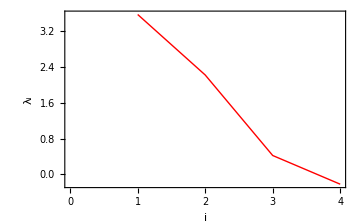
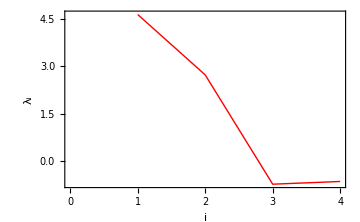
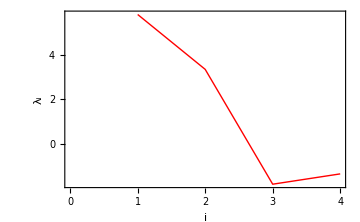
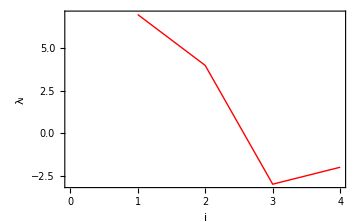

```mathematica
Table[ListPlot[N[Eigenvalues[redM13[4,t]]],Joined->True,Axes->False,Frame->True,FrameLabel->{i,Subscript[λ, i]},PlotStyle->{Red,Thick},FrameStyle->Directive[Thick,Black],ImageSize->Medium,LabelStyle->{18,Bold}],{t,0.5,2,0.5}]
```